```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["../../SpinningTrajectory.wl"]
```

## Separatrix

```mathematica
a=0.95
e=0.5
x=0.5
```

0.95

0.5

0.5

```mathematica
listδp=Table[1.0*10^k,{k,-4,1,0.01}];
```

```mathematica
listLinearParts=Table[KerrSpinLinearParts[a,KerrGeoSeparatrix[a,e,x]+listδp[[i]],e,x],{i,1,Length[listδp]}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{-4.78087×10^6,557575.,131135.},{1.1309×10^7,-1.31892×10^6,-310196.},{1.88036×10^7,-2.19299×10^6,-515768.}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

```mathematica
listLinearParts[[1]]
```

<|Ω1CTilde→{0.00406831,0.0360331,0.0491836},C1CTilde→{-0.0275357,-0.110813,1.76224},pex1CTilde→{-1.32169,-0.0142281,0.0717989},J1C→{-3.98984,-0.12118,0},CTilde1C→{0.0275357,0.110813,-1.76224},CTilde1pex→{0.0162947,-0.124971,1.1255},CTilde1Ω→{0.0623043,-0.30749,3.57887},Ω1C→{-300950.,711886.,1.18367×10^6},Ω1pex→{8.9422,-21.1201,-35.1263},C1pex→{-0.011241,-0.235784,2.88774},pex1C→{-29754.6,3685.58,0.1556},C1Ω→{0.0347686,-0.418303,5.34111},pex1Ω→{0.114002,0.522638,-0.130843},J1CTilde→{-8.00276,0.252637,-0.110813},J1pex→{-7.81767,0.538732,-0.235784},J1Ω→{-7.19996,1.10329,-0.418303},Ω1J→{-550758.,1.3028×10^6,2.16618×10^6},C1J→{0.0682848,0.,0.584535},CTilde1J→{0.0958205,0.110813,-1.17771},pex1J→{-54450.9,6745.29,0.133197},dΩdC→{{-4.78087×10^6,557575.,131135.},{1.1309×10^7,-1.31892×10^6,-310196.},{1.88036×10^7,-2.19299×10^6,-515768.}},dJdC→{{71.5626,-5.96748,-1.53422},{0.291808,-0.691198,0.173222},{0,1,0}},dpexdC→{{-472647.,55123.5,12964.8},{58554.2,-6827.36,-1605.81},{-0.0697395,0.29364,-0.0301787}}|>

```mathematica
<<MaTeX`
```

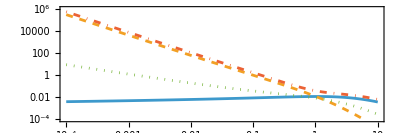

```mathematica
ListLogLogPlot[{
Table[{listδp[[i]],Abs@listLinearParts[[i]]["Ω1CTilde"][[1]]},{i,1,Length[listδp]}],
Table[{listδp[[i]],Abs@listLinearParts[[i]]["Ω1C"][[1]]},{i,1,Length[listδp]}],
Table[{listδp[[i]],Abs@listLinearParts[[i]]["Ω1pex"][[1]]},{i,1,Length[listδp]}],
Table[{listδp[[i]],Abs@listLinearParts[[i]]["Ω1J"][[1]]},{i,1,Length[listδp]}]
},Joined->True,Axes->False,Frame->True,FrameLabel->{MaTeX["p-p_s"],Rotate[MaTeX["\\Omega^1_r"],-Pi/2]},PlotRange->{{10^-4,10},{10^-4,10^6}},AspectRatio->1/3,FrameStyle->Black,PlotStyle->{Automatic,Dashed,Dotted,DotDashed}]
```

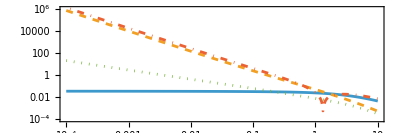

```mathematica
ListLogLogPlot[{
Table[{listδp[[i]],Abs@listLinearParts[[i]]["Ω1CTilde"][[2]]},{i,1,Length[listδp]}],
Table[{listδp[[i]],Abs@listLinearParts[[i]]["Ω1C"][[2]]},{i,1,Length[listδp]}],
Table[{listδp[[i]],Abs@listLinearParts[[i]]["Ω1pex"][[2]]},{i,1,Length[listδp]}],
Table[{listδp[[i]],Abs@listLinearParts[[i]]["Ω1J"][[2]]},{i,1,Length[listδp]}]
},Joined->True,Axes->False,Frame->True,FrameLabel->{MaTeX["p-p_s"],Rotate[MaTeX["\\Omega^1_z"],-Pi/2]},PlotRange->{{10^-4,10},{10^-4,10^6}},AspectRatio->1/3,FrameStyle->Black,PlotStyle->{Automatic,Dashed,Dotted,DotDashed}]
```

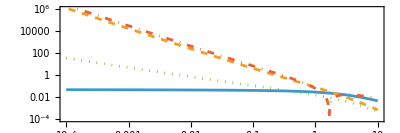

```mathematica
ListLogLogPlot[{
Table[{listδp[[i]],Abs@listLinearParts[[i]]["Ω1CTilde"][[3]]},{i,1,Length[listδp]}],
Table[{listδp[[i]],Abs@listLinearParts[[i]]["Ω1C"][[3]]},{i,1,Length[listδp]}],
Table[{listδp[[i]],Abs@listLinearParts[[i]]["Ω1pex"][[3]]},{i,1,Length[listδp]}],
Table[{listδp[[i]],Abs@listLinearParts[[i]]["Ω1J"][[3]]},{i,1,Length[listδp]}]
},Joined->True,Axes->False,Frame->True,FrameLabel->{MaTeX["p-p_s"],Rotate[MaTeX["\\Omega^1_\\phi"],-Pi/2]},PlotRange->{{10^-4,10},{10^-4,10^6}},AspectRatio->1/3,FrameStyle->Black,PlotStyle->{Automatic,Dashed,Dotted,DotDashed}]
```

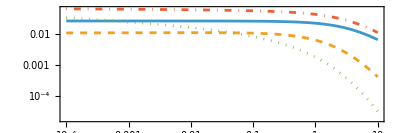

```mathematica
ListLogLogPlot[{
Table[{listδp[[i]],Abs@listLinearParts[[i]]["C1CTilde"][[1]]},{i,1,Length[listδp]}],
Table[{listδp[[i]],Abs@listLinearParts[[i]]["C1pex"][[1]]},{i,1,Length[listδp]}],
Table[{listδp[[i]],Abs@listLinearParts[[i]]["C1Ω"][[1]]},{i,1,Length[listδp]}],
Table[{listδp[[i]],Abs@listLinearParts[[i]]["C1J"][[1]]},{i,1,Length[listδp]}]
},Joined->True,Axes->False,Frame->True,FrameLabel->{MaTeX["p-p_s"],Rotate[MaTeX["E^1"],-Pi/2]},PlotRange->{{10^-4,10},All},AspectRatio->1/3,FrameStyle->Black,PlotStyle->{Automatic,Dashed,Dotted,DotDashed}]
```

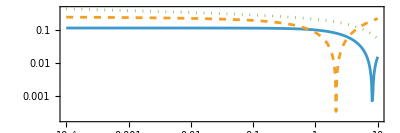

```mathematica
ListLogLogPlot[{
Table[{listδp[[i]],Abs@listLinearParts[[i]]["C1CTilde"][[2]]},{i,1,Length[listδp]}],
Table[{listδp[[i]],Abs@listLinearParts[[i]]["C1pex"][[2]]},{i,1,Length[listδp]}],
Table[{listδp[[i]],Abs@listLinearParts[[i]]["C1Ω"][[2]]},{i,1,Length[listδp]}],
Table[{listδp[[i]],Abs@listLinearParts[[i]]["C1J"][[2]]},{i,1,Length[listδp]}]
},Joined->True,Axes->False,Frame->True,FrameLabel->{MaTeX["p-p_s"],Rotate[MaTeX["L_z^1"],-Pi/2]},PlotRange->{{10^-4,10},All
},AspectRatio->1/3,FrameStyle->Black,PlotStyle->{Automatic,Dashed,Dotted,DotDashed}]
```

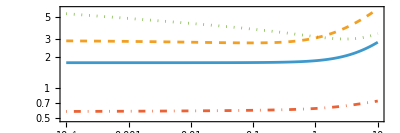

```mathematica
ListLogLogPlot[{
Table[{listδp[[i]],Abs@listLinearParts[[i]]["C1CTilde"][[3]]},{i,1,Length[listδp]}],
Table[{listδp[[i]],Abs@listLinearParts[[i]]["C1pex"][[3]]},{i,1,Length[listδp]}],
Table[{listδp[[i]],Abs@listLinearParts[[i]]["C1Ω"][[3]]},{i,1,Length[listδp]}],
Table[{listδp[[i]],Abs@listLinearParts[[i]]["C1J"][[3]]},{i,1,Length[listδp]}]
},Joined->True,Axes->False,Frame->True,FrameLabel->{MaTeX["p-p_s"],Rotate[MaTeX["K^1"],-Pi/2]},PlotRange->{{10^-4,10},All
},AspectRatio->1/3,FrameStyle->Black,PlotStyle->{Automatic,Dashed,Dotted,DotDashed}]
```

## Circular

```mathematica
Clear[e]
```

```mathematica
a=0.95
p=12.0
x=0.5
```

0.95

12.

0.5

```mathematica
liste=Table[1.0*10^k,{k,-3,-0.005,0.005}];
```

```mathematica
listLinearPartse=Table[KerrSpinLinearParts[a,p,liste[[i]],x],{i,1,Length[liste]}];
```

```mathematica
listLinearPartse[[1]]
```

<|Ω1CTilde→{0.00685414,0.00868036,0.00904641},C1CTilde→{-0.0110125,-0.00762767,2.52463},pex1CTilde→{-3.2767,-5.08898×10^-6,0.00478567},J1C→{-1.00913,-0.0988193,0},CTilde1C→{0.0110125,0.00762767,-2.52463},CTilde1pex→{0.00992126,0.191997,2.85304},CTilde1Ω→{0.0111199,-0.0995932,0.894928},Ω1C→{-0.00008236,0.00135455,0.00185404},Ω1pex→{0.000919891,-0.000457505,-0.000871913},C1pex→{-0.00109126,0.184369,5.37767},pex1C→{-6.388,278.718,0.0485937},C1Ω→{0.000107353,-0.107221,3.41956},pex1Ω→{-2.92766,135.494,-0.0337463},J1CTilde→{-2.01825,0.231209,-0.00762767},J1pex→{-2.01825,0.458814,0.184369},J1Ω→{-1.52768,0.427011,-0.107221},Ω1J→{-0.012889,-0.0147882,-0.0149026},C1J→{0.020776,0.,0.707509},CTilde1J→{0.0317885,0.00762767,-1.81712},pex1J→{-6.31395,557.437,0.0355086},dΩdC→{{-0.618178,0.000265656,0.0000518217},{-0.762373,-0.00182022,-0.000429258},{-0.786491,-0.00227004,-0.000588673}},dJdC→{{54.173,-0.355165,-0.164482},{0.333563,-0.761727,0.129877},{0,1,0}},dpexdC→{{-33.6656,2.56035,1.09326},{14962.4,-98.0957,-45.4295},{-0.0543831,0.228981,-0.0168977}}|>

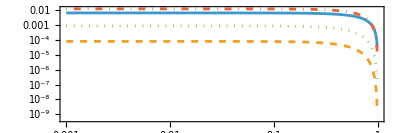

```mathematica
ListLogLogPlot[{
Table[{liste[[i]],Abs@listLinearPartse[[i]]["Ω1CTilde"][[1]]},{i,1,Length[liste]}],
Table[{liste[[i]],Abs@listLinearPartse[[i]]["Ω1C"][[1]]},{i,1,Length[liste]}],
Table[{liste[[i]],Abs@listLinearPartse[[i]]["Ω1pex"][[1]]},{i,1,Length[liste]}],
Table[{liste[[i]],Abs@listLinearPartse[[i]]["Ω1J"][[1]]},{i,1,Length[liste]}]
},Joined->True,Axes->False,Frame->True,FrameLabel->{MaTeX["e"],Rotate[MaTeX["\\Omega^1_r"],-Pi/2]},PlotRange->{{10^-3,1},All},AspectRatio->1/3,FrameStyle->Black,PlotStyle->{Automatic,Dashed,Dotted,DotDashed}]
```

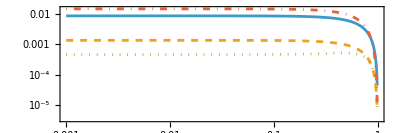

```mathematica
ListLogLogPlot[{
Table[{liste[[i]],Abs@listLinearPartse[[i]]["Ω1CTilde"][[2]]},{i,1,Length[liste]}],
Table[{liste[[i]],Abs@listLinearPartse[[i]]["Ω1C"][[2]]},{i,1,Length[liste]}],
Table[{liste[[i]],Abs@listLinearPartse[[i]]["Ω1pex"][[2]]},{i,1,Length[liste]}],
Table[{liste[[i]],Abs@listLinearPartse[[i]]["Ω1J"][[2]]},{i,1,Length[liste]}]
},Joined->True,Axes->False,Frame->True,FrameLabel->{MaTeX["e"],Rotate[MaTeX["\\Omega^1_z"],-Pi/2]},PlotRange->{{10^-3,1},All},AspectRatio->1/3,FrameStyle->Black,PlotStyle->{Automatic,Dashed,Dotted,DotDashed}]
```

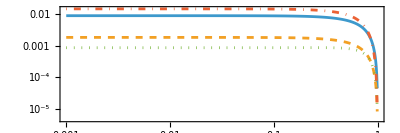

```mathematica
ListLogLogPlot[{
Table[{liste[[i]],Abs@listLinearPartse[[i]]["Ω1CTilde"][[3]]},{i,1,Length[liste]}],
Table[{liste[[i]],Abs@listLinearPartse[[i]]["Ω1C"][[3]]},{i,1,Length[liste]}],
Table[{liste[[i]],Abs@listLinearPartse[[i]]["Ω1pex"][[3]]},{i,1,Length[liste]}],
Table[{liste[[i]],Abs@listLinearPartse[[i]]["Ω1J"][[3]]},{i,1,Length[liste]}]
},Joined->True,Axes->False,Frame->True,FrameLabel->{MaTeX["e"],Rotate[MaTeX["\\Omega^1_\\phi"],-Pi/2]},PlotRange->{{10^-3,1},All},AspectRatio->1/3,FrameStyle->Black,PlotStyle->{Automatic,Dashed,Dotted,DotDashed}]
```

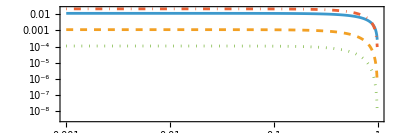

```mathematica
ListLogLogPlot[{
Table[{liste[[i]],Abs@listLinearPartse[[i]]["C1CTilde"][[1]]},{i,1,Length[liste]}],
Table[{liste[[i]],Abs@listLinearPartse[[i]]["C1pex"][[1]]},{i,1,Length[liste]}],
Table[{liste[[i]],Abs@listLinearPartse[[i]]["C1Ω"][[1]]},{i,1,Length[liste]}],
Table[{liste[[i]],Abs@listLinearPartse[[i]]["C1J"][[1]]},{i,1,Length[liste]}]
},Joined->True,Axes->False,Frame->True,FrameLabel->{MaTeX["e"],Rotate[MaTeX["E^1"],-Pi/2]},PlotRange->{{10^-3,1},All},AspectRatio->1/3,FrameStyle->Black,PlotStyle->{Automatic,Dashed,Dotted,DotDashed}]
```

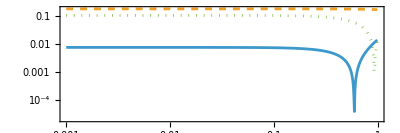

```mathematica
ListLogLogPlot[{
Table[{liste[[i]],Abs@listLinearPartse[[i]]["C1CTilde"][[2]]},{i,1,Length[liste]}],
Table[{liste[[i]],Abs@listLinearPartse[[i]]["C1pex"][[2]]},{i,1,Length[liste]}],
Table[{liste[[i]],Abs@listLinearPartse[[i]]["C1Ω"][[2]]},{i,1,Length[liste]}],
Table[{liste[[i]],Abs@listLinearPartse[[i]]["C1J"][[2]]},{i,1,Length[liste]}]
},Joined->True,Axes->False,Frame->True,FrameLabel->{MaTeX["e"],Rotate[MaTeX["L_z^1"],-Pi/2]},PlotRange->{{10^-3,1},All
},AspectRatio->1/3,FrameStyle->Black,PlotStyle->{Automatic,Dashed,Dotted,DotDashed}]
```

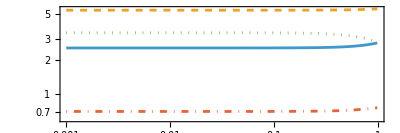

```mathematica
ListLogLogPlot[{
Table[{liste[[i]],Abs@listLinearPartse[[i]]["C1CTilde"][[3]]},{i,1,Length[liste]}],
Table[{liste[[i]],Abs@listLinearPartse[[i]]["C1pex"][[3]]},{i,1,Length[liste]}],
Table[{liste[[i]],Abs@listLinearPartse[[i]]["C1Ω"][[3]]},{i,1,Length[liste]}],
Table[{liste[[i]],Abs@listLinearPartse[[i]]["C1J"][[3]]},{i,1,Length[liste]}]
},Joined->True,Axes->False,Frame->True,FrameLabel->{MaTeX["e"],Rotate[MaTeX["K^1"],-Pi/2]},PlotRange->{{10^-3,1},All
},AspectRatio->1/3,FrameStyle->Black,PlotStyle->{Automatic,Dashed,Dotted,DotDashed}]
```

## Equatorial

```mathematica
Clear[x]
```

```mathematica
a=0.95
p=12.0
e=0.5
```

0.95

12.

0.5

```mathematica
listz1=Table[1.0*10^k,{k,-3,-0.005,0.005}];
```

```mathematica
listLinearPartsx=Table[KerrSpinLinearParts[a,p,e,Sqrt[1-listz1[[i]]^2]],{i,1,Length[listz1]}];
```

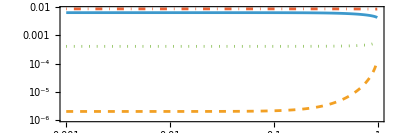

```mathematica
ListLogLogPlot[{
Table[{listz1[[i]],Abs@listLinearPartsx[[i]]["Ω1CTilde"][[1]]},{i,1,Length[listz1]}],
Table[{listz1[[i]],Abs@listLinearPartsx[[i]]["Ω1C"][[1]]},{i,1,Length[listz1]}],
Table[{listz1[[i]],Abs@listLinearPartsx[[i]]["Ω1pex"][[1]]},{i,1,Length[listz1]}],
Table[{listz1[[i]],Abs@listLinearPartsx[[i]]["Ω1J"][[1]]},{i,1,Length[listz1]}]
},Joined->True,Axes->False,Frame->True,FrameLabel->{MaTeX["e"],Rotate[MaTeX["\\Omega^1_r"],-Pi/2]},PlotRange->{{10^-3,1},All},AspectRatio->1/3,FrameStyle->Black,PlotStyle->{Automatic,Dashed,Dotted,DotDashed}]
```

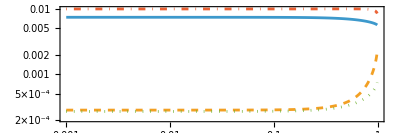

```mathematica
ListLogLogPlot[{
Table[{listz1[[i]],Abs@listLinearPartsx[[i]]["Ω1CTilde"][[2]]},{i,1,Length[listz1]}],
Table[{listz1[[i]],Abs@listLinearPartsx[[i]]["Ω1C"][[2]]},{i,1,Length[listz1]}],
Table[{listz1[[i]],Abs@listLinearPartsx[[i]]["Ω1pex"][[2]]},{i,1,Length[listz1]}],
Table[{listz1[[i]],Abs@listLinearPartsx[[i]]["Ω1J"][[2]]},{i,1,Length[listz1]}]
},Joined->True,Axes->False,Frame->True,FrameLabel->{MaTeX["e"],Rotate[MaTeX["\\Omega^1_z"],-Pi/2]},PlotRange->{{10^-3,1},All},AspectRatio->1/3,FrameStyle->Black,PlotStyle->{Automatic,Dashed,Dotted,DotDashed}]
```

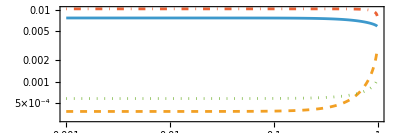

```mathematica
ListLogLogPlot[{
Table[{listz1[[i]],Abs@listLinearPartsx[[i]]["Ω1CTilde"][[3]]},{i,1,Length[listz1]}],
Table[{listz1[[i]],Abs@listLinearPartsx[[i]]["Ω1C"][[3]]},{i,1,Length[listz1]}],
Table[{listz1[[i]],Abs@listLinearPartsx[[i]]["Ω1pex"][[3]]},{i,1,Length[listz1]}],
Table[{listz1[[i]],Abs@listLinearPartsx[[i]]["Ω1J"][[3]]},{i,1,Length[listz1]}]
},Joined->True,Axes->False,Frame->True,FrameLabel->{MaTeX["e"],Rotate[MaTeX["\\Omega^1_\\phi"],-Pi/2]},PlotRange->{{10^-3,1},All},AspectRatio->1/3,FrameStyle->Black,PlotStyle->{Automatic,Dashed,Dotted,DotDashed}]
```

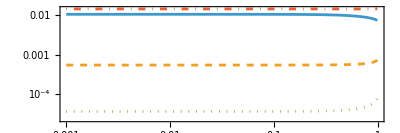

```mathematica
ListLogLogPlot[{
Table[{listz1[[i]],Abs@listLinearPartsx[[i]]["C1CTilde"][[1]]},{i,1,Length[listz1]}],
Table[{listz1[[i]],Abs@listLinearPartsx[[i]]["C1pex"][[1]]},{i,1,Length[listz1]}],
Table[{listz1[[i]],Abs@listLinearPartsx[[i]]["C1Ω"][[1]]},{i,1,Length[listz1]}],
Table[{listz1[[i]],Abs@listLinearPartsx[[i]]["C1J"][[1]]},{i,1,Length[listz1]}]
},Joined->True,Axes->False,Frame->True,FrameLabel->{MaTeX["e"],Rotate[MaTeX["E^1"],-Pi/2]},PlotRange->{{10^-3,1},All},AspectRatio->1/3,FrameStyle->Black,PlotStyle->{Automatic,Dashed,Dotted,DotDashed}]
```

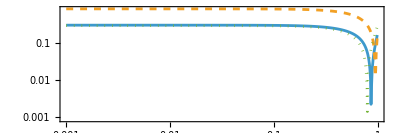

```mathematica
ListLogLogPlot[{
Table[{listz1[[i]],Abs@listLinearPartsx[[i]]["C1CTilde"][[2]]},{i,1,Length[listz1]}],
Table[{listz1[[i]],Abs@listLinearPartsx[[i]]["C1pex"][[2]]},{i,1,Length[listz1]}],
Table[{listz1[[i]],Abs@listLinearPartsx[[i]]["C1Ω"][[2]]},{i,1,Length[listz1]}],
Table[{listz1[[i]],Abs@listLinearPartsx[[i]]["C1J"][[2]]},{i,1,Length[listz1]}]
},Joined->True,Axes->False,Frame->True,FrameLabel->{MaTeX["e"],Rotate[MaTeX["L_z^1"],-Pi/2]},PlotRange->{{10^-3,1},All
},AspectRatio->1/3,FrameStyle->Black,PlotStyle->{Automatic,Dashed,Dotted,DotDashed}]
```

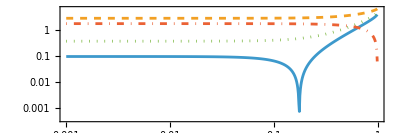

```mathematica
ListLogLogPlot[{
Table[{listz1[[i]],Abs@listLinearPartsx[[i]]["C1CTilde"][[3]]},{i,1,Length[listz1]}],
Table[{listz1[[i]],Abs@listLinearPartsx[[i]]["C1pex"][[3]]},{i,1,Length[listz1]}],
Table[{listz1[[i]],Abs@listLinearPartsx[[i]]["C1Ω"][[3]]},{i,1,Length[listz1]}],
Table[{listz1[[i]],Abs@listLinearPartsx[[i]]["C1J"][[3]]},{i,1,Length[listz1]}]
},Joined->True,Axes->False,Frame->True,FrameLabel->{MaTeX["e"],Rotate[MaTeX["K^1"],-Pi/2]},PlotRange->{{10^-3,1},All
},AspectRatio->1/3,FrameStyle->Black,PlotStyle->{Automatic,Dashed,Dotted,DotDashed}]
```